```mathematica
SOI=Import["/users/pp/github/context/Mathematica/SOIM/data/soi.txt", "table"];
TSID=Import["/users/pp/github/context/Mathematica/SOIM/data/tsi.txt", "table"];
QBO=Import["/users/pp/github/context/Mathematica/SOIM/data/qbo20.txt", "table"];
QBO70=Import["/users/pp/github/context/Mathematica/SOIM/data/qbo.txt", "table"];
CW=Import["/users/pp/github/context/Mathematica/SOIM/data/cw.txt", "table"];
CW1=Import["/users/pp/github/context/Mathematica/SOIM/data/cw1_1930.txt", "table"];
CW0=Import["/users/pp/github/context/Mathematica/SOIM/data/cw1.txt", "table"];
NINO34=Import["/users/pp/github/context/Mathematica/SOIM/data/nino34ke.txt", "table"];
tahiti=Import["/users/pp/github/context/Mathematica/SOIM/data/tahiti.txt", "table"];
darwin=Import["/users/pp/github/context/Mathematica/SOIM/data/darwin0.txt", "table"];
```

75.4216

6.47885

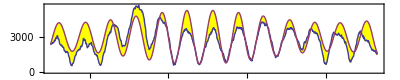

```mathematica
CWF =0.9698; cw[x_] := Sin[CWF*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  
CWD = MeanFilter[CW1[[All,2]],5];
CWM = Table[{1880+i, 1770*cw[i-1.42]+3000},{i,50+1/12,133-0/12, 1/12}];
CWT = Table[{1880+50+i/12, CWD[[i]]},{i,1,(83+0/12)*12, 1}];
100*Correlation[CWT,CWM][[2,2]] 
2*Pi/CWF
ListLinePlot[{CWT,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

{char t,7.22158,0.0257585, Years from,1880.17,to,1980.25,CC,70.2663,72.2317,1.96535}

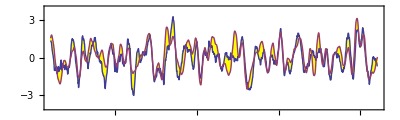

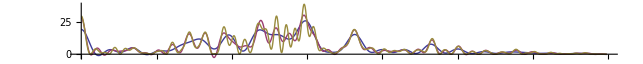

4.36332

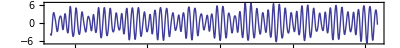

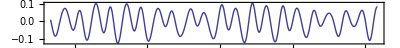

7.27221

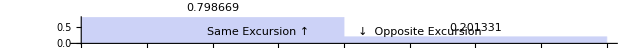

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.05*Sin[0.123*x+0.13])+1.45] ; 
(* CWF =0.9698; cwp[x_] := Sin[CWF*(x+2.)+ 0.119*Sin[0.36*(x+6.8)] +0.5] *(1+0.31*Sin[0.093*x-0.2]) ;  *)
tsi[x_]=Cos[2*Pi/10.6*x];
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1203; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.757;  dilate[x_] := -(0.03*Cos[2*Pi*x-0.89]);
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.483;
Hill[x_] := CF*(1-0.19*Cos[CWF*x-.08/CWF]+0.0001*x);
Osc[x_] := -1.6*(0.03*Cos[2*Pi/OSC*x+4.3] +0.056*Cos[2*Pi/(2*OSC)*x+0.2] - 0.051*Cos[2*Pi*x/(3.0*OSC)-0.6] +.04*Cos[2*Pi*x/(6.0*OSC)-3.9]);
QBOG[x_]:=7.0*qbo[x+0.252]+0.013*Cos[2*Pi*x/(7.0)+0.1]+3.46*Cos[2*Pi*x/(2.33391)-1.51] -1.2*Cos[2*Pi*x/(1.952)-0.98] + 0.37*Cos[2*Pi*x/(2.9)-0.37];
(* CWG[x_]:= If[x<100,0.07*Cos[2*Pi*x/(CWR)+1.0+0.27*Sin[0.524*x-0.3]],0.052*Cos[2*Pi*x/(CWR)+1.7] ]  +0.03*Cos[2*Pi*x/(2*CWR)+2.1];    *)
CWG[x_]:= 0.071*Cos[2*Pi*x/(CWR)+0.000022*x*x+1+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.02*Sin[2*Pi*x/(5.83)-0.3]; (* ,   *)
(* CWG[x_]:=0.1*cw[x+1]; *)
QTO[x_]:= 0.42*Cos[2*Pi*x/(3.801)-1] - 0*0.12*Sin[2*Pi*x/(3.52)-1.4] ;
RHS[x_] :=  0.93*QBOG[x]*(1+0.05*tsi[x-6.8])+CWG[x]+QTO[x]+Osc[x+1.2] + 
           0.043*Cos[2*Pi*x/(18.031)-0.2]+ 0*0.015*Cos[2*Pi*x/(8.85)+0.25]+ 0.4*Cos[2*Pi*x/(1/(1-1/6.483))+0.22] ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.12*(y[x])^2 == 1.03*RHS[x-0.01] ,        y'[TR]==0.0, y[TR]==0.1}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, -1.01*qbo[x+1.03]+First[-2.18*y[x+dilate[x]+0.67] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.3]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,1200,400}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/0.12/12
 RHST = Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]; 
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
ListLinePlot[{Table[{1880.0+x, CWG[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
2*Pi/0.072/12
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

```mathematica
2
```

2

{char t,7.24073,0.0673619, Years from,1880.17,to,1980.,CC,54.6152,54.5167,54.6152,0.0985439}

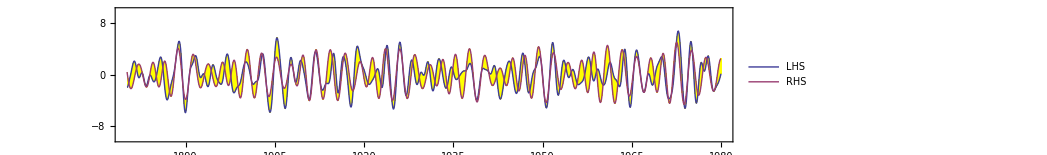

```mathematica
Window1 = 9;  
R = GaussianFilter[GaussianFilter[(1*GaussianFilter[darwin[[All,2]],Window1-0])-(1*GaussianFilter[tahiti[[All,2]],Window1-0]),Window1-2],Window1-4];
lhs=Table[{1880.0+x,  12*12*(2*R[[x*12]]-R[[x*12+1]]-R[[x*12-1]])-Hill[x]*R[[x*12]]  },{x,STRT/12,LNGTH/12+0, 1/12}];     
rhs=Table[{1880.0+x, -0.53*RHS[x+0.6]},  {x,STRT/12,LNGTH/12+0, 1/12}];     
SBIN = Abs[Sign[lhs[[All,2]]]- Sign[rhs[[All,2]]]]/2; 
(* OldCC = NewCC; NewCC = 50*(1.0-N[Total[SBIN]/Length[SBIN]]) + 50*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs]; *)
OldCC = NewCC; NewCC = 100*Correlation[lhs,rhs][[2,2]];  Var = Variance[lhs]-Variance[rhs];
CC = 100*Correlation[lhs,rhs][[2,2]];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",CC, OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{lhs,rhs},PlotRange->{-10,10},Frame->True,Axes->True, Filling->{1->{{2},Yellow}}, PlotLegends->{"LHS","RHS"},AspectRatio->0.2] 
(* missing qbo *)
```

76.9756

{0.,3027.02}

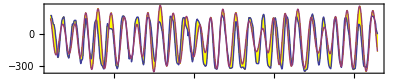

```mathematica
QBOM = Table[{1953.0+x, -47*(0.95*QBOG[72.63+x]+1.*QTO[71.6+x])-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];   (* 72.62 76.139 *)
OFFS:=72.54;
QBOM = Table[{1953.0+x, -36*(1.3*QBOG[OFFS+x+0.0889]+1.2*QTO[OFFS-0.51+x+0.0889])-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];   (* 72.62 76.139 *)
QBOM = Table[{1953.0+x, -36*RHS[OFFS+x]-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];   (* 72.62 76.139 *)

QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```

72.2296

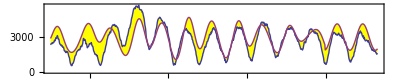

```mathematica
CWD = MeanFilter[CW1[[All,2]],5];
CWM = Table[{1880+i, 16000*CWG[i-1.67]+3000},{i,50+1/12,133-0/12, 1/12}];
CWT = Table[{1880+50+i/12, CWD[[i]]},{i,1,(83+0/12)*12, 1}];
100*Correlation[CWT,CWM][[2,2]] 
ListLinePlot[{CWT,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]
```

```mathematica
1/(1-1/6.483)
```

```mathematica
1.49*0.03
```

```mathematica
0.0447
100/27.5
```

0.0447

3.63636

{char t,7.23737,0.196146, Years from,1880.17,to,2013.58,CC,78.3982,58.4761,-19.9221}

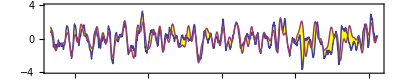

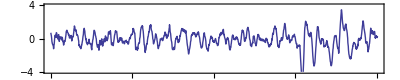

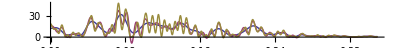

12.4666

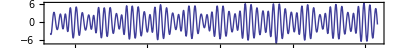

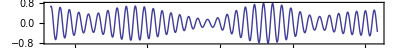

2.2376

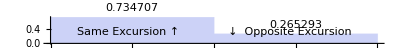

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1603; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.7537; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+4.3] +0.056*Cos[2*Pi/(2*OSC)*x+0.21] - 0.05*Cos[2*Pi*x/(3.0*OSC)-0.6] +.039*Cos[2*Pi*x/(6.0*OSC)-3.9]);
Semidiurnal[x_] := 0.026*Cos[2*Pi*x/(SEMI)+0.33]-0.12*Cos[2*Pi*x/(SEMI/2)+0.0];
QTO[x_]:= 0.44*Cos[2*Pi*x/(3.801)-1] - 0.22*Sin[2*Pi*x/(3.52)-1.6] -0.14*Sin[2*Pi/4*x-1.2];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Saros[x_] := 0.045*Cos[2*Pi*x/(18.031)-0.2];
Hill[x_] := CF*(1-0.22*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(0.95*QBOG[x]+QTO[x])+0.9*CWG[x-0.0]+Diurnal[x+1.2] + Saros[x] + Semidiurnal[x+0.1]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 1.03*RHS[x-0.01] , y'[TR]==-0.001, y[TR]==0.11}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.223*QBOG[x+0.64]+First[-(1)*2.2*y[x+0.681] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,1200,400}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/0.042/12
 RHST = Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]; 
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
ListLinePlot[{Table[{1880.0+x, QTO[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"QTO"}]
2*Pi/0.234/12
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

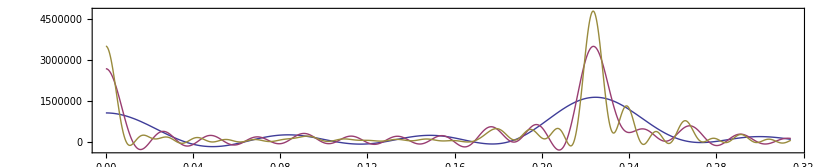

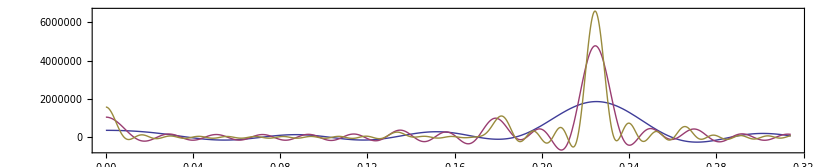

0.137753

0.14875

```mathematica
(* QBOM = Table[{1953.0+x, -40*(0.93*QBOG[72.62+x]+1.*QTO[71.48+x])-74},{x,1/12,61.25+1/12, 1/12}];  *)
Q = MeanFilter[QBO[[All,2]],3];   (* 72.62 76.139 *)
Plot[Evaluate@Table[PowerSpectralDensity[Q,ω,i],{i,100,500,200}],{ω,0,π/10},PlotRange->All,Frame->True,Axes->True,AspectRatio->0.2] 
Plot[Evaluate@Table[PowerSpectralDensity[QBOM,ω,i],{i,100,500,200}],{ω,0,π/10},PlotRange->All,Frame->True,Axes->True,AspectRatio->0.2] 
2*Pi/3.801/12
2*Pi/3.52/12
```

{char t,4.81898,0.03432, Years from,1880.17,to,1980.25,CC,78.3428,70.2663,-8.0765}

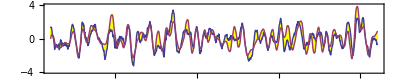

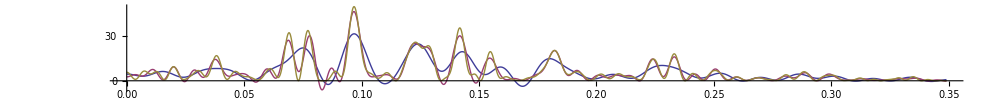

5.51157

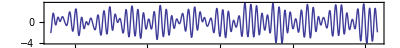

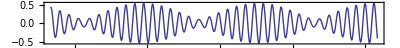

2.25689

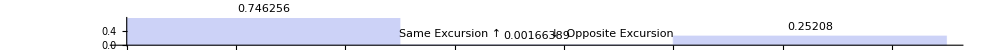

```mathematica
(* -------------------------------------------------------------- Higher CF ------------------------------------------------- *)
WinHiFilter = 5;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
tsi[x_]:=Cos[2*Pi/10.6*x];
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1203; ENDY=1880+LNGTH/12; 
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 1.7;  dilate[x_] := -(0.05*Cos[2*Pi*x-0.8]);
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4825; SEMI := 8.85;
Hill[x_] := CF*(1+0.15*Cos[CWF*x-.0/CWF]+0.0001*x);
Diurnal[x_] := -1.6*(0.03*Cos[2*Pi/OSC*x+4.3] +0.05*Cos[2*Pi/(2*OSC)*x+0.2] - 0.033*Cos[2*Pi*x/(3.0*OSC)-0.6] +.015*Cos[2*Pi*x/(6.0*OSC)-3.9]);
Semidiurnal[x_] := 0.021*Cos[2*Pi*x/(SEMI)+0.25]-0.08*Cos[2*Pi*x/(SEMI/2)+0.4];
QTO[x_]:= 0.32*Cos[2*Pi*x/(3.8)-0.95] - 0.22*Sin[2*Pi*x/(3.52)-1.2] ;
QBOG[x_]:=3.6*qbo[x+.24]+.014*Cos[2*Pi*x/7+.1]+3.2*Cos[2*Pi*x/2.3339-1.51] -1.2*Cos[2*Pi*x/1.952-.98]-.03*Cos[2*Pi*x/2.9+1.0];
CWG[x_]:= If[x<118, 0.071*Cos[2*Pi*x/(CWR)+1.0+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.08*Sin[2*Pi*x/(5.83)-0.0],
                    0.071*Cos[2*Pi*x/(CWR)+2.0]]  - 0*0.7*Cos[2*Pi*x/(1/(1-1/CWR))+0.32]; (* ,   *)
Saros[x_] := 0.2*Cos[2*Pi*x/(18.031)-0.3];
RHS[x_] := (0.93*QBOG[x]+1.*QTO[x+0.04])-1.5*CWG[x]-0.5*CWG[x/2-1.8]+4.0*Diurnal[x+0.8] + Saros[x] + 0.9*Semidiurnal[x] -0.2*Cos[2*Pi*x/(7.33)+0.5] ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x]+0.08*(y[x])^2 == 1*RHS[x-0.05] , y'[TR]==0.1, y[TR]==0.01}, y, {x, 0, 260}];   
SOIM=Table[{1880.0+x, 0.0*QBOG[x-0.03]+First[-2*y[x+dilate[x]+0.61] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];     
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
Plot[Evaluate@Table[PowerSpectralDensity[SDIF,ω,i],{i,400,1200,400}],{ω,0,π/9},PlotRange->All,AspectRatio->0.1]
2*Pi/0.095/12
 RHST = Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]; 
ListLinePlot[{Table[{1880.0+x, RHS[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"RHS"}]
ListLinePlot[{Table[{1880.0+x, QTO[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
2*Pi/0.232/12
SBIN = Abs[Sign[SOIT[[All,2]]]- Sign[SOIM[[All,2]]]]/2; 
Histogram[SBIN, Automatic, "Probability", LabelingFunction->Above, AspectRatio->0.05,  ChartLabels->Placed[{"Same Excursion ↑              ↓  Opposite Excursion"},Bottom]]
```

{char t,7.23737,-0.474325, Years from,1880.17,to,1913.33,CC,54.9606,65.1892,10.2286}

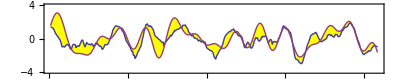

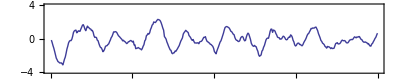

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=400; ENDY=1880+LNGTH/12;  (* 400 *)
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.7537; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+4.3] +0.056*Cos[2*Pi/(2*OSC)*x+0.21] - 0.05*Cos[2*Pi*x/(3.0*OSC)-0.6] +.039*Cos[2*Pi*x/(6.0*OSC)-3.9]);
Semidiurnal[x_] := 0.026*Cos[2*Pi*x/(SEMI)+0.33]-0.12*Cos[2*Pi*x/(SEMI/2)+0.0];
QTO[x_]:= 0.44*Cos[2*Pi*x/(3.801)-1] - 0.22*Sin[2*Pi*x/(3.52)-1.6] -0.14*Sin[2*Pi/4*x-1.2];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Saros[x_] := 0.045*Cos[2*Pi*x/(18.031)-0.2];
Hill[x_] := CF*(1-0.22*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(1.2*QBOG[x+0.06]+0*QTO[x])+1.1*CWG[x-0.2]+0.6*Diurnal[x+1.5] + 1.2*Saros[x-1] + 1.3*Semidiurnal[x+0.5]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 1.03*RHS[x-0.01] , y'[TR]==-0.001, y[TR]==0.11}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.223*QBOG[x+0.64]+First[-(1)*2.2*y[x+0.681] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
```

{char t,7.23737,-0.958395, Years from,1880.17,to,1980.,CC,72.1113,60.0442,-12.0671}

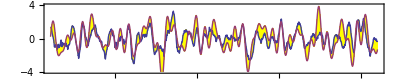

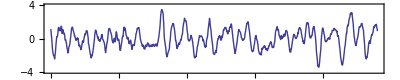

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1200; ENDY=1880+LNGTH/12;  (* 400 *)
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.7537; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.8] +0.056*Cos[2*Pi/(2*OSC)*x+1.5] - 0.07*Cos[2*Pi*x/(3.0*OSC)-0.7] +.01*Cos[2*Pi*x/(6.0*OSC)-4.6]);
Semidiurnal[x_] := 0.04*Cos[2*Pi*x/(SEMI)+0.3]-0.14*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.44*Cos[2*Pi*x/(3.801)-1] - 0.22*Sin[2*Pi*x/(3.52)-1.6] -0.14*Sin[2*Pi/4*x-1.2];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Saros[x_] := 0.045*Cos[2*Pi*x/(18.031)-0.2];
Hill[x_] := CF*(1-0.0*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(1.19*QBOG[x+0.07]+0*QTO[x])+1.2*CWG[x-0.19]+0.7*Diurnal[x+1.6] + 1.5*Saros[x-1] + 1.3*Semidiurnal[x+0.6]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 1.03*RHS[x-0.01] , y'[TR]==0.001, y[TR]==0.11}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.23*QBOG[x+0.64]+First[-(1)*2.3*y[x+0.63] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
```

{char t,7.2552,-1.18241, Years from,1880.17,to,1913.33,CC,69.408,81.839,12.4309}

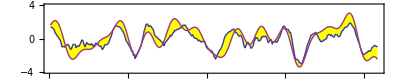

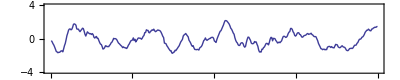

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=400; ENDY=1880+LNGTH/12;  (* 400 *)
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.75; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.8] +0.056*Cos[2*Pi/(2*OSC)*x+1.5] - 0.07*Cos[2*Pi*x/(3.0*OSC)-0.7] +.01*Cos[2*Pi*x/(6.0*OSC)-4.6]);
Semidiurnal[x_] := 0.04*Cos[2*Pi*x/(SEMI)+0.3]-0.14*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.44*Cos[2*Pi*x/(3.801)-1] - 0.22*Sin[2*Pi*x/(3.52)-1.6] -0.14*Sin[2*Pi/4*x-1.2];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Saros[x_] := 0.045*Cos[2*Pi*x/(18.031)-0.2];
Hill[x_] := CF*(1-0.0*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(1.23*QBOG[x+0.089]+1.3*QTO[x])+1.2*CWG[x-0.1]+0.6*Diurnal[x+1.8] + 1.2*Saros[x-0.3] + 1.4*Semidiurnal[x+0.6]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 0.98*RHS[x-0.02] , y'[TR]==0.01, y[TR]==0.1}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.23*QBOG[x+0.66]+First[-(1)*2.2*y[x+0.628] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
```

{char t,7.26004,0.0737657, Years from,1880.17,to,1913.33,CC,87.2242,87.2242,0.}

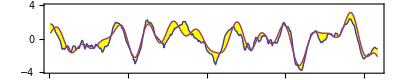

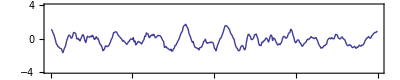

```mathematica
(* -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=400; ENDY=1880+LNGTH/12;  (* 400 *)
SOIT = Table[{1880+i/12, -1.27*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.749; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Diurnal[x_] := -1.49*(0.029*Cos[2*Pi/OSC*x+3.7] +0.06*Cos[2*Pi/(2*OSC)*x+1.6] - 0.083*Cos[2*Pi*x/(3.0*OSC)-0.7] );
Semidiurnal[x_] := 0.037*Cos[2*Pi*x/(SEMI)+0.4]-0.16*Cos[2*Pi*x/(SEMI/2)-0.12];
QTO[x_]:= 0.33*Cos[2*Pi*x/(3.801)-1] - 0.21*Sin[2*Pi*x/(3.52)-1.2] -0.4*Sin[2*Pi/4*x-1.0];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Saros[x_] := 0.045*Cos[2*Pi*x/(18.031)-0.21];
Hill[x_] := CF*(1-0.0*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(1.29*QBOG[x+0.089]+1.25*QTO[x])+1.17*CWG[x-0.06]+0.61*Diurnal[x+1.9] + 0.7*Saros[x-0.5] + 1.4*Semidiurnal[x+0.65]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 0.98*RHS[x-0.02] , y'[TR]==0.01, y[TR]==0.1}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.23*QBOG[x+0.66]+First[-(1)*2.2*y[x+0.628] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
```

{char t,7.2552,-1.25135, Years from,1880.17,to,1980.,CC,76.9619,58.299,-18.6629}

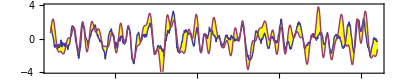

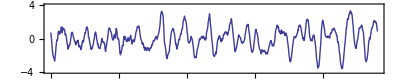

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1200; ENDY=1880+LNGTH/12;  (* 400 *)
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.75; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.8] +0.06*Cos[2*Pi/(2*OSC)*x+1.5] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.7] );
Semidiurnal[x_] := 0.039*Cos[2*Pi*x/(SEMI)+0.3]-0.15*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.33*Cos[2*Pi*x/(3.801)-1] - 0.21*Sin[2*Pi*x/(3.52)-1.2] -0.4*Sin[2*Pi/4*x-1.0];
QTO[x_]:= 0.25*Cos[2*Pi*x/(3.9)+0.6] ;
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Saros[x_] := 0.045*Cos[2*Pi*x/(18.031)-0.2];
Hill[x_] := CF*(1-0.0*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(1.3*QBOG[x+0.089]+1.25*QTO[x])+1.19*CWG[x-0.07]+0.62*Diurnal[x+1.8] + 0.8*Saros[x-0.3] + 1.4*Semidiurnal[x+0.65]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 0.98*RHS[x-0.02] , y'[TR]==0.01, y[TR]==0.1}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.23*QBOG[x+0.66]+First[-(1)*2.2*y[x+0.628] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
```

{char t,7.2552,-0.921663, Years from,1880.17,to,1980.,CC,78.351,57.0135,-21.3375}

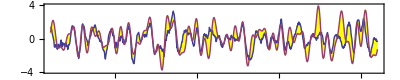

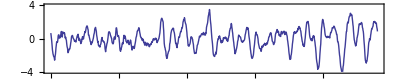

```mathematica
(* -------------------------------------------------------------- GOOD ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1200; ENDY=1880+LNGTH/12;  (* 400 *)
SOIT = Table[{1880+i/12, -R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.75; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Semidiurnal[x_] := 0.029*Cos[2*Pi*x/(SEMI)+0.6]-0.15*Cos[2*Pi*x/(SEMI/2)-0.5];
QTO[x_]:= 0.34*Cos[2*Pi*x/(3.801)-1] - 0.21*Sin[2*Pi*x/(3.52)-1.2] -0.4*Sin[2*Pi/4*x-1.0];
QTO[x_]:= 0.25*Cos[2*Pi*x/(3.9)+0.6] ;
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Hill[x_] := CF*(1-0.0*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(1.3*QBOG[x+0.089]+1.8*QTO[x-0.01])+1.29*CWG[x-0.08]+  1.4*Semidiurnal[x+0.7]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 0.98*RHS[x-0.02] , y'[TR]==0.01, y[TR]==0.1}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.23*QBOG[x+0.66]+First[-(1)*2.2*y[x+0.628] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
```

```mathematica
0
```

{char t,7.26004,-0.48168, Years from,1880.17,to,1980.,CC,86.1893,59.0646,-27.1247}

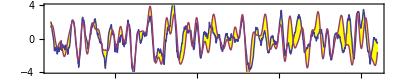

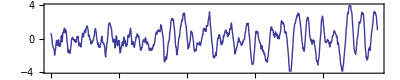

3.89744

152.

```mathematica
(* -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 6;  (* 8 *)
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1200; ENDY=1880+LNGTH/12;  (* 400 *)
SOIT = Table[{1880+i/12, -1.45*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.749; 
OSC := 9.305;     TR=52.0;  CWF := 0.757;  CWR := 6.4826; SEMI := 8.85;  (* 6.4826 *)
Diurnal[x_] := -1.49*(0.029*Cos[2*Pi/OSC*x+3.7] +0.06*Cos[2*Pi/(2*OSC)*x+1.6] - 0*0.083*Cos[2*Pi*x/(3.0*OSC)-0.7] );
Semidiurnal[x_] := 0.037*Cos[2*Pi*x/(SEMI)+0.4]-0.16*Cos[2*Pi*x/(SEMI/2)-0.12];
QTO[x_]:= 0.33*Cos[2*Pi*x/(3.801)-1] - 0.21*Sin[2*Pi*x/(3.52)-1.2] -0.4*Sin[2*Pi/4*x-1.0];
QTO[x_]:= 0.36*Cos[2*Pi*x/(3.9)+0.2] - 0.33*Sin[2*Pi*x/(3.52)-1.4];
(* QTO[x_]:= 0.2*Cos[2*Pi*x/(3.7)-0.3]; *)
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
Hill[x_] := CF*(1-0.0*Cos[CWF*x-.12/CWF ]-0.0*QTO[x+0]-0*1.1*CWG[x+0.7]);
RHS[x_] :=(1.29*QBOG[x+0.089]+2.3*QTO[x])+1.17*CWG[x-0.06]+0.61*Diurnal[x+1.9] + 1.4*Semidiurnal[x+0.65]  ;  
SOLN=NDSolve[{y''[x]+Hill[x]*y[x] == 0.98*RHS[x-0.02] , y'[TR]==0.01, y[TR]==0.1}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.23*QBOG[x+0.66]+First[-(1)*2.2*y[x+0.628] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];    (* 2.18 *) 
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]

1/((1/3.8+1/4)/2)
1/((1/3.8-1/4)/2)
```

{char t,7.24073,0.176706, Years from,1881.,to,1913.33,CC,92.9145,92.9145,0.}

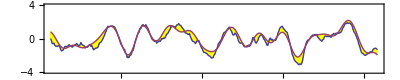

```mathematica
(* First 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=12; STRTY=1880+STRT/12; SEP=0.0; LNGTH=400; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.753;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  

Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9]+0*0.014*Sin[2*Pi/8.0*x-0.15];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.3*QBOG[x+0.0889]+1.2*QTO[x+0.0889])+1.16*CWG[x-0.04]+0.58*Diurnal[x+2.1]+1.23*Semidiurnal[x+0.6] ;
SOLN=NDSolve[{y''[x]+CF*y[x]+0*0.03*y'[x] == 0.93*RHS[x-0.02]*(1+0*0.02*Sin[2*Pi/9.33*x-1.5]) , 
             y'[TR]==-0.001, y[TR]==0.13}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+First[-(1)*2.2*y[x+0.63] /. SOLN]},{x,-0*13 +STRT/12,LNGTH/12+0, 1/12}];   
SOIM=Table[{1880.0+x, -0.232*RHS[x+0.601]+First[-(1)*2.2*y[x+0.63] /. SOLN]},{x,-0*13 +STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,7.24073,-0.0292193, Years from,1988.33,to,2013.33,CC,45.9132,45.8922,-0.0210262}

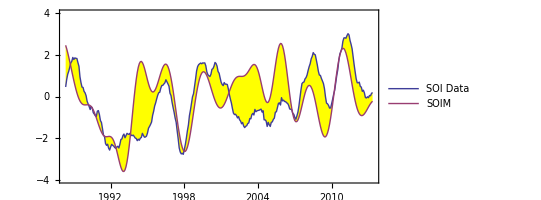

```mathematica
(* First 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=1300; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1600; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.753;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9]+0*0.014*Sin[2*Pi/8.0*x-0.15];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.3*QBOG[x+0.0889]+1.2*QTO[x+0.0889])+1.16*CWG[x-0.04]+0.58*Diurnal[x+2.1]+1.23*Semidiurnal[x+0.6] ;

SOLN=NDSolve[{y''[x]+CF*y[x]+0.07*y'[x] == 0.8*RHS[x-0.05], y'[TR]==1.0, y[TR]==0.3}, y, {x, -50, 260}]; 
SHFT=0.61;
SOIM=Table[{1880.0+x, 2*(-0.25*RHS[x+SHFT-0.13]+First[-(1)*2.1*y[x+SHFT] /. SOLN])},{x,-0*13 +STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.5]
```

76.8856

{0.,54.8591}

-0.470559

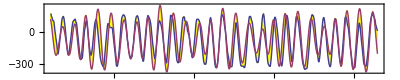

```mathematica
OFFS:=72.545;
QBOM = Table[{1953.0+x, -34.16*RHS[OFFS+x]-72},{x,1/12,61.25+1/12, 1/12}];  
Q = MeanFilter[QBO[[All,2]],4];  
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
SDIF = QBOT[[All,2]]-QBOM[[All,2]];  
Variance[QBOT]-Variance[QBOM]
Mean[SDIF]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}, AspectRatio->0.1]
```

{char t,7.2552,-0.483055, Years from,1913.33,to,1946.67,CC,57.4275,73.6355,16.208}

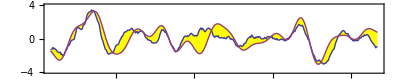

```mathematica
(* Second 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=400; STRTY=1880+STRT/12; SEP=0.0; LNGTH=800; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.75;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Diurnal[x_] := -1.49*(0.05*Cos[2*Pi/OSC*x+3.6] -0.09*Cos[2*Pi/(2*OSC)*x+1.7] - 0.1*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.032*Cos[2*Pi*x/(SEMI)+0.1]-0.16*Cos[2*Pi*x/(SEMI/2)-0.4];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.2*QBOG[x+0.088]+1.43*QTO[x+0.71])+1.4*CWG[x+0.02]+0.5*Diurnal[x+2.5]+0.9*Semidiurnal[x-0.1] ;
SOLN=NDSolve[{y''[x]+CF*y[x]+0.00*y[x] == 0.89*RHS[x-0.02] , y'[TR]==0.0, y[TR]==-0.25}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+First[-(1)*2.2*y[x+0.63] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,7.2552,-0.310171, Years from,1946.67,to,1980.,CC,90.1179,90.1179,0.}

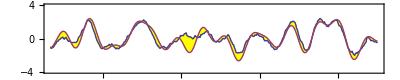

```mathematica
(* Third 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=800; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1200; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.75;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.05*Cos[2*Pi/OSC*x+3.6] -0.1*Cos[2*Pi/(2*OSC)*x+1.7] - 0.12*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.02*Cos[2*Pi*x/(SEMI)-0.2]-0.14*Cos[2*Pi*x/(SEMI/2)-0.6];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.25*QBOG[x+0.088]+1.38*QTO[x-0.36])+1.4*CWG[x+0.08]+0.51*Diurnal[x+2.5]+0.9*Semidiurnal[x+0.5] ;
SOLN=NDSolve[{y''[x]+CF*y[x]+0.00*y[x] == 0.93*RHS[x-0.02] , y'[TR]==0.18, y[TR]==0.25}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+First[-(1)*2.2*y[x+0.63] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,7.24073,0.0169078, Years from,1913.33,to,1946.67,CC,76.943,76.9913,0.0482327}

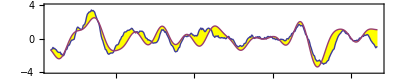

```mathematica
(* Second 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=400; STRTY=1880+STRT/12; SEP=0.0; LNGTH=800; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.753;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.05*Cos[2*Pi/OSC*x+3.7] +0.05*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.037*Cos[2*Pi*x/(SEMI)+0.45]-0.15*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.13*QBOG[x+0.11]+1.5*QTO[x+0.7])+1.01*CWG[x+0.1]+0.5*Diurnal[x+1.6]+1.4*Semidiurnal[x+0.5] ;
SOLN=NDSolve[{y''[x]+CF*y[x]+0.00*y[x] == 0.93*RHS[x-0.02] , y'[TR]==-0.000, y[TR]==0.13}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+First[-(1)*2.2*y[x+0.63] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

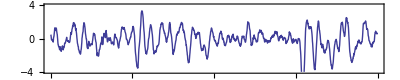

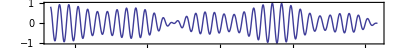

```mathematica
SDIF = SOIT[[All,2]]-SOIM[[All,2]];  
ListLinePlot[SDIF, AspectRatio->0.2,Frame->True,Axes->False,PlotRange->{-4,4}]
ListLinePlot[{Table[{1880.0+x, QTO[x]},{x,1/12,135.0, 1/12}]}, AspectRatio->0.1, Frame->True, Axes->False, PlotLegends->{"CW"}]
```

```mathematica
tsi[x_]:=Cos[2*Pi/10.6*x];
*(1-0.15*tsi[x-3.9])
```

{char t,6.98132,-0.671625, Years from,1880.17,to,2013.33,CC,50.6975,46.5816,-4.11593}

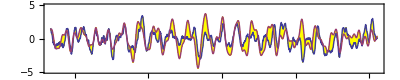

```mathematica
(* -------------------------------------------------------------- Change of boundary conditions ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1600; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.81;  OSC := 9.305;  TR=108.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(0.9*1.3*QBOG[x+0.0889]+0.4*1.2*QTO[x+0.0889])+1.67*1.16*CWG[x-0.04]+1.0*0.58*Diurnal[x+2.1]+1.4*1.23*Semidiurnal[x+0.6] ;
SOLN=NDSolve[{y''[x]+CF*y[x]-0.01*y[x] == +0.9*RHS[x-0.02] -0*DiracDelta[x-108], y'[TR]==-3.38, y[TR]==-0.18}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+1.8/2*(1-0*0.52*Cos[2*Pi*x/150+2.6])*First[-(1)*2.2*y[x+0.72] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,6.98132,1.15569, Years from,1988.33,to,2013.33,CC,51.3464,51.4028,0.0564264}

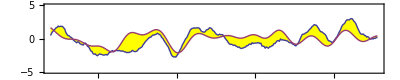

```mathematica
(* -------------------------------------------------------------- Change of boundary conditions ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=1300; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1600; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.81;  OSC := 9.305;  TR=108.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(0.9*1.3*QBOG[x+0.0889]+0.4*1.2*QTO[x+0.0889])+1.67*1.16*CWG[x-0.04]+1.0*0.58*Diurnal[x+2.1]+1.4*1.23*Semidiurnal[x+0.6] ;
SOLN=NDSolve[{y''[x]+CF*y[x]+0.0*y'[x] == +0.9*RHS[x-0.02] -0*DiracDelta[x-108], y'[TR]==-3.38, y[TR]==-0.18}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+1.8/2*(1-0*0.52*Cos[2*Pi*x/150+2.6])*First[-(1)*2.2*y[x+0.72] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-5,5+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,6.98132,-2.69251, Years from,1880.17,to,2013.33,CC,14.6766,34.0641,19.3876}

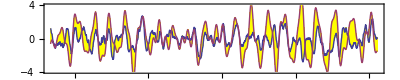

```mathematica
(* -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1600; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -0.95*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.81;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(0.9*1.3*QBOG[x+0.0889]+0.4*1.2*QTO[x+0.0889])+1.67*1.16*CWG[x-0.04]+1.0*0.58*Diurnal[x+2.1]+1.4*1.23*Semidiurnal[x+0.6] ;
SOLN=NDSolve[{y''[x]+CF*y[x]-0.01*y[x] == +0.9*RHS[x-0.02] -0*DiracDelta[x-108], y'[TR]==-0.001, y[TR]==0.13}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+First[-(1)*2.2*y[x+0.72] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,6.98132,-0.83295, Years from,1880.17,to,1913.33,CC,30.2905,30.9639,0.673444}

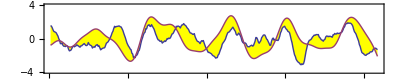

```mathematica
(* -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=2; STRTY=1880+STRT/12; SEP=0.0; LNGTH=400; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.81;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9];
QBOG[x_]:=7*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(0.9*1.3*QBOG[x+0.0889]+0.4*1.2*QTO[x+0.0889])+1.67*1.16*CWG[x-0.04]+1.0*0.58*Diurnal[x+2.1]+1.4*1.23*Semidiurnal[x+0.6] ;
SOLN=NDSolve[{y''[x]+CF*y[x]-0.01*y[x] == +0.9*RHS[x-0.02] -0*DiracDelta[x-108], y'[TR]==+0.02, y[TR]==0.2}, y, {x, 0, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+1.8/2*(1-0*0.52*Cos[2*Pi*x/150+2.6])*First[-(1)*2.2*y[x+0.63] /. SOLN]},{x,STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

{char t,7.24073,-5.64183, Years from,1979.,to,2013.33,CC,32.6529,32.6561,0.00313624}

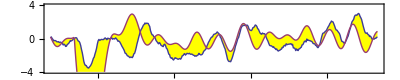

```mathematica
(* First 1/4 -------------------------------------------------------------- EXCELLENT ------------------------------------------------- *)
WinHiFilter = 8;  
QB=2.695; qbo[x_] :=  Cos[QB*(x+0.24*Sin[0.524*x+2.85]-0.06*Sin[0.123*x+0.13])+1.45] ; 
R = (1*MeanFilter[darwin[[All,2]],WinHiFilter])-(1*MeanFilter[tahiti[[All,2]],WinHiFilter]); 
STRT=-12+1200; STRTY=1880+STRT/12; SEP=0.0; LNGTH=1600; ENDY=1880+LNGTH/12;  
SOIT = Table[{1880+i/12, -1.2*R[[i]]+SEP},{i,STRT,LNGTH,1}];        (* scaled SOI Data Table from NCAR *)
CF = 0.753;  OSC := 9.305;  TR=52.0;  CWR := 6.4826;  SEMI := 8.85;  
Diurnal[x_] := -1.49*(0.03*Cos[2*Pi/OSC*x+3.7] +0.07*Cos[2*Pi/(2*OSC)*x+1.7] - 0.08*Cos[2*Pi*x/(3.0*OSC)-0.6] );
Semidiurnal[x_] := 0.036*Cos[2*Pi*x/(SEMI)+0.45]-0.17*Cos[2*Pi*x/(SEMI/2)-0.1];
QTO[x_]:= 0.3*Cos[2*Pi*x/(3.801)-0.58] - 0.21*Sin[2*Pi*x/(3.52)-2.0] -0.49*Sin[2*Pi/4.0*x-0.9] ;
QBOG[x_]:=7.0*qbo[x+.245]+.013*Cos[2*Pi*x/7+.1]+3.45*Cos[2*Pi*x/2.33391-1.51] -1.2*Cos[2*Pi*x/1.952-.98]+.39*Cos[2*Pi*x/2.9-.3];
CWG[x_]:= If[x<118, 0.072*Cos[2*Pi*x/(CWR)+0.99+0.27*Sin[0.524*x-0.3]]+0.031*Cos[2*Pi*x/(2*CWR)+2.4]+ 0.021*Sin[2*Pi*x/(5.83)-0.3], 0.071*Cos[2*Pi*x/(CWR)+2.0]];
RHS[x_] :=(1.3*QBOG[x+0.0889]+1.2*QTO[x+0.0889])+1.16*CWG[x-0.04]+0.58*Diurnal[x+2.1]+1.23*Semidiurnal[x+0.6] + 9.3*DiracDelta[x-102.1];
SOLN=NDSolve[{y''[x]+CF*y[x]+0.91*y'[x] == 0.93*RHS[x-0.02] , y'[TR]==-01.00, y[TR]==0.13}, y, {x, -50, 260}]; 
SOIM=Table[{1880.0+x, -0.27*QBOG[x+0.68]+First[-(1)*2.2*y[x+0.63] /. SOLN]},{x,-0*13 +STRT/12,LNGTH/12+0, 1/12}];   
OldCC = NewCC; NewCC = 100*Correlation[SOIT,SOIM][[2,2]];  Var = Variance[SOIT]-Variance[SOIM];
Print[{"char t",2*Pi/Sqrt[CF],Var[[2]]," Years from",N[STRTY],"to",N[ENDY],"CC",OldCC,NewCC,NewCC-OldCC}]
ListLinePlot[{SOIT,SOIM},PlotRange->{-4,4+SEP},Frame->True,Axes->False, Filling->{1->{{2},Yellow}},  PlotLegends->{"SOI Data","SOIM"},AspectRatio->0.2]
```

72.41

6.47885

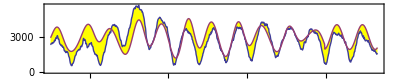

76.6611

{0.,1103.24}

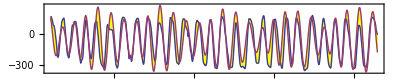

```mathematica
CWD = MeanFilter[CW1[[All,2]],5];
CWM = Table[{1880+i, 15000*CWG[i-1.6]+3000},{i,50+1/12,133-0/12, 1/12}];
CWT = Table[{1880+50+i/12, CWD[[i]]},{i,1,(83+0/12)*12, 1}];
100*Correlation[CWT,CWM][[2,2]] 
2*Pi/CWF
ListLinePlot[{CWT,CWM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"CW", "Model"}]

OFFS:=72.64;
QBOM = Table[{1953.0+x, -36*(1.3*QBOG[OFFS+x]+1.2*QTO[OFFS-0*.51+x])-50},{x,1/12,61.25+1/12, 1/12}];  Q = MeanFilter[QBO[[All,2]],3];   (* 72.62 76.139 *)
QBOT = Table[{QBOM[[i,1]], Q[[i]]},{i,1,12*61.25+1, 1}];        
100*Correlation[QBOT,QBOM][[2,2]]
Variance[QBOT]-Variance[QBOM]
ListLinePlot[{QBOT, QBOM}, AspectRatio->0.2, Filling->{1->{{2},Yellow}}, Frame->True, Axes->False, PlotLegends->{"QBO", "Model"}]
```